```mathematica
OTC=ArrayReshape[Reverse[{542,482,553,493,551,628,691,710,696,635,641,648,707,601,582,603,595,598,673,586,507,418,373,299,283,259,220,197,169,142,128,111,100,96,94,88,81,80,72}],{39,1}];
```

```mathematica
dates=ArrayReshape[Reverse[DateRange[DateList["01 June 2017"],DateList["01 May 1998"],{-6,"Month"}]],{39,1,6}];
```

```mathematica
a=Join[dates,OTC,2];
```

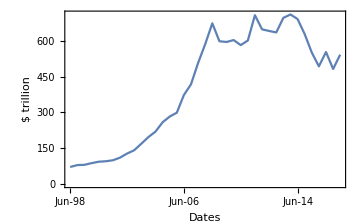

```mathematica
img=Show[{DateListPlot[a,AxesLabel->{"$ trillion","A"},DateTicksFormat->{"MonthNameShort", "-", "YearShort"},FrameTicks->{{Automatic,Automatic},{{"June 1, 1998","June 1, 2002","June 1, 2006","June 1, 2010","June 1, 2014","June 1, 2017"},None}},ImageSize->Medium,FrameLabel->{"Dates","$ trillion"}]},Epilog->Inset[Framed[Column[{LineLegend[{Blue},{"OTC Market Size"}]}],RoundingRadius->0,FrameMargins->None],Scaled[{.23,.88}],Background->White]]
```

```mathematica
Export["C:\\Users\\Miguel\\Documents\\GitHub\\Thesis\\Images\\OTC.eps",img,"eps"];
```

```mathematica
NotebookSave[]
```

```mathematica
Max[OTC]
```

710